# Quiz 3 Review

## Find Limits using power series

```mathematica
Limit[(Sin[x]-x)/x^3,x->0]
```

-1/6

```mathematica
Limit[(x^2*Exp[x])/(Cos[x]-1),x->0]
```

-2

```mathematica
Limit[Log[x]/(x-1),x->0]
```

∞

```mathematica
Limit[(x)/(Exp[3x]-1),x->0]
```

1/3

```mathematica
Limit[x/ArcTan[4x],x->0]
```

1/4

## Find the sum

```mathematica
Sum[(-1)^n/(n+1),{n,0,Infinity}]
```

Log[2]

```mathematica
LogOfOnePlusX[x_]:=Sum[(-1)^n*x^(n+1)/(n+1),{n,0,Infinity}]
```

```mathematica
Function[x,∑_(n=0)^∞ ((-1)^n x^(n+1))/(n+1)]
```

Function[x,∑_(n=0)^∞ ((-1)^n x^(n+1))/(n+1)]

```mathematica
LogOfOnePlusX[1]
```

Log[2]

```mathematica
Sum[3^n/(7^n*n!),{n,0,Infinity}]
```

ⅇ^(3/7)

## Taylor Series representations

```mathematica
Series[Exp[x],{x,0,9}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+O[x]^10

```mathematica
Series[Exp[-x^2],{x,0,19}]
```

1-x^2+x^4/2-x^6/6+x^8/24-x^10/120+x^12/720-x^14/5040+x^16/40320-x^18/362880+O[x]^20

```mathematica
Integrate[Exp[-x^2],{x,0,1}]
```

1/2 √π Erf[1]

```mathematica
N[1/2 √π Erf[1]]
```

0.746824

```mathematica
Sum[(-1)^n/(n!*(2n+1)),{n,0,Infinity}]
```

1/2 √π Erf[1]

```mathematica
N[1/2 √π Erf[1]]
```

0.746824

## Find the Taylor Polynomial T3[x] at a=1

```mathematica
T3[x_]=Series[2*Log[x+1]-Log[x],{x,1,3}]//Normal
```

1/4 (-1+x)^2-1/4 (-1+x)^3+2 Log[2]

```mathematica
T3[Sqrt[2]]//N
```

1.41142

```mathematica
f[x_] :=(2*Log[x+1]-Log[x])
```

```mathematica
Function[x,2 Log[x+1]-Log[x]]
```

Function[x,2 Log[x+1]-Log[x]]

```mathematica
f[Sqrt[2]]//N
```

1.41617

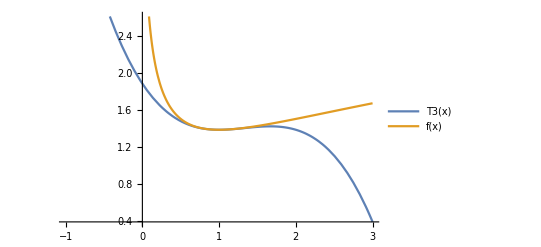

```mathematica
Plot[{T3[x],f[x]},{x,-1,3},PlotLegends->"Expressions"]
```

## Determine Interval of Convergence

```mathematica
SumConvergence[(4x-5)^n/(3^n*n),n]
```

Abs[-5+4 x]<3

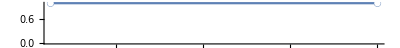

```mathematica
NumberLinePlot[SumConvergence[(4x-5)^n/(3^n*n),n],x]
```

```mathematica
SumConvergence[(4x-5)^n/(n!),n]
```

True

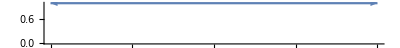

```mathematica
NumberLinePlot[SumConvergence[(4x-5)^n/(n!),n],x]
```

```mathematica
SumConvergence[(4x-5)^n/(n^3*2^(n+3)),n]
```

Abs[-5/2+2 x]<1

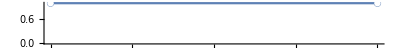

```mathematica
NumberLinePlot[SumConvergence[(4x-5)^n/(n^3*2^(n+3)),n],x]
```

```mathematica
SumConvergence[(x-5)^n/(3^n*n^2),n]
```

Abs[-5+x]<3

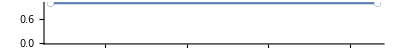

```mathematica
NumberLinePlot[SumConvergence[(x-5)^n/(3^n*n^2),n],x]
```

```mathematica
SumConvergence[(x+6)^n/(2n)!,n]
```

True

```mathematica
NumberLinePlot[SumConvergence[(x+6)^n/(2n)!,n],x]
```

-Graphics-

## Find power series representation

```mathematica
Series[1/(4+x),{x,0,9}]
```

1/4-x/16+x^2/64-x^3/256+x^4/1024-x^5/4096+x^6/16384-x^7/65536+x^8/262144-x^9/1048576+O[x]^10

```mathematica
Series[x^2/(4+x),{x,0,9}]
```

x^2/4-x^3/16+x^4/64-x^5/256+x^6/1024-x^7/4096+x^8/16384-x^9/65536+O[x]^10

```mathematica
Series[Log[(4+x)],{x,0,9}]
```

2 Log[2]+x/4-x^2/32+x^3/192-x^4/1024+x^5/5120-x^6/24576+x^7/114688-x^8/524288+x^9/2359296+O[x]^10

```mathematica
Integrate[Series[x^3*Log[4+x],{x,0,9}],x]
```

1/4 Log[4] x^4+x^5/20-x^6/192+x^7/1344-x^8/8192+x^9/46080-x^10/245760+O[x]^11

```mathematica
Series[x^3*Log[4+x^2],{x,0,19}]
```

2 Log[2] x^3+x^5/4-x^7/32+x^9/192-x^11/1024+x^13/5120-x^15/24576+x^17/114688-x^19/524288+O[x]^20

```mathematica
Series[Log[4+x^2],{x,0,19}]
```

2 Log[2]+x^2/4-x^4/32+x^6/192-x^8/1024+x^10/5120-x^12/24576+x^14/114688-x^16/524288+x^18/2359296+O[x]^20

```mathematica
Series[Exp[2x]+5*Exp[-3x],{x,0,9}]
```

6-13 x+(49 x^2)/2-(127 x^3)/6+(421 x^4)/24-(1183 x^5)/120+(3709 x^6)/720-(10807 x^7)/5040+(4723 x^8)/5760-(97903 x^9)/362880+O[x]^10

```mathematica
Integrate[Series[x^2*Exp[-5x^3],{x,0,19}],x]
```

x^3/3-(5 x^6)/6+(25 x^9)/18-(125 x^12)/72+(125 x^15)/72-(625 x^18)/432+O[x]^21

```mathematica
Series[x^4/(3+x^3),{x,0,19}]
```

x^4/3-x^7/9+x^10/27-x^13/81+x^16/243-x^19/729+O[x]^20

```mathematica
Series[x*ArcTan[x^4],{x,0,29}]
```

x^5-x^13/3+x^21/5-x^29/7+O[x]^30